```mathematica
Clear["Global`*"]
```

```mathematica
Get["TSPnew3"];
```

```mathematica
PartLoop={5->4,4->2,2->1,1->5}
```

{5→4,4→2,2→1,1→5}

```mathematica
RevPartLoop=EdgeRules[ReverseGraph[Graph[PartLoop]]]
```

{5→1,4→5,2→4,1→2}

```mathematica
hp=Table[
If[MemberQ[PartLoop,Ruleg[[i]]],1,0]+If[MemberQ[RevPartLoop,Ruleg[[i]]],-1,0],
{i,EdgeCount[Gin]}
](* h part *)
```

{-1,0,0,1,0,1,0,0,0,1}

```mathematica
PLA=Area[Polygon[Pin[[
ConnectedComponents[PartLoop][[1]]
]]
]](* Part Loop Area *)
```

10.5

```mathematica
EdgePos[Edge_]:=(
FirstPosition[EdgeRules[Gin],Edge,
FirstPosition[
EdgeRules[Gin],
EdgeRules[
ReverseGraph[{Edge}]
][[1]]
]
][[1]]
) (* Edge Position *)
```

```mathematica
SumPD=Sum[PD[[EdgePos[PartLoop[[i]]]]],{i,Length[PartLoop]}](* Sum Point Distance *)
```

13.9594

```mathematica
sRemoval=-hp PLA PD/SumPD
```

{1.68192,0.,0.,-3.7609,0.,-2.19296,0.,0.,0.,-2.86421}

```mathematica
Curr2=Transpose[h].Inverse[h.r.Transpose[h]].(h.sRemoval+U)(* 誘導起電力行列を考慮した電流を求める式 *)
```

{0.128895,0.32532,0.348797,-0.105418,-0.174382,-0.0378028,-0.0832895,-0.0679409,0.43176,0.243053}

```mathematica
CurrRemoval=Transpose[h].Inverse[h.r.Transpose[h]].(h.sRemoval)(* 誘導起電力行列を考慮した電流を求める式 *)
```

{0.75218,-5.55112×10^-17,6.76542×10^-17,-0.75218,0.,-0.75218,1.11022×10^-16,1.38778×10^-16,1.66533×10^-16,-0.75218}

```mathematica
Gout2=Graph[Table[If[Curr2[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout2][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout2][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout2]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[StyleForm[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[StyleForm[Abs[Curr2[[i]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gout2][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gout2][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

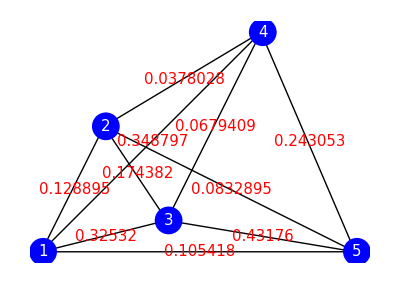

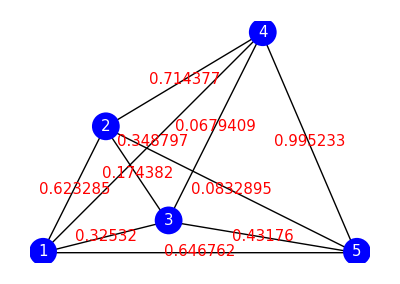

```mathematica
GoutRemoval=Graph[Table[If[CurrRemoval[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

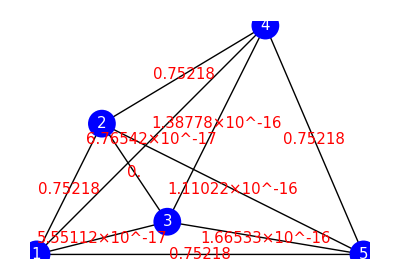

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[GoutRemoval][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[GoutRemoval][[i]]}][[2]]]]},
{i,Length[EdgeRules[GoutRemoval]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[StyleForm[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[StyleForm[Abs[CurrRemoval[[i]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

```mathematica
GoutRemoval=Graph[Table[If[CurrRemoval2[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

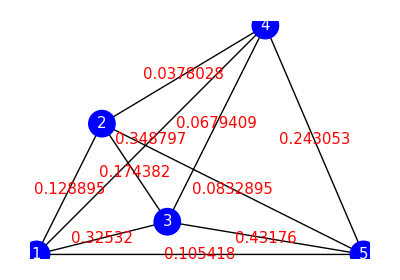

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[GoutRemoval][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[GoutRemoval][[i]]}][[2]]]]},
{i,Length[EdgeRules[GoutRemoval]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[StyleForm[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[StyleForm[Abs[CurrRemoval[[i]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```